## Дополнительные функции:

```mathematica
MakeTable[{points_,fValues_,norms_}]:=Module[{gridLabel,gridData},
gridLabel={"k","(X^k)","f(X^k)","Sum[α_i*e_i]"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i≤Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],4]]<>", "<>ToString[SetAccuracy[points[[i,2]],4]]<>" )"];
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,4];
(*в 4-м столбце-значение нормы невязки*)
For[i=1,i≤Length[points],i++,gridData[[i,4]]="( "<>ToString[SetAccuracy[norms[[i,1]],4]]<>", "<>ToString[SetAccuracy[norms[[i,2]],4]]<>" )"
];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
];
PlotMethod[func_,setX_,setY_,{points_,fValues_}]:=Module[{},
ContourPlot[func[{x,y}],setX,setY,Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{func[{x,y}]}]],FrameStyle->Thick,ImageSize->350,PlotPoints->100,Epilog->{Purple,Thickness[0.001],Arrowheads[.02],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.015],Point[points[[1;;-1]]],Yellow,Point[points[[-1]]]}]
];
PlotNorms[norms_]:=Module[{},
ListLogPlot[norms,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full, MeshStyle->Directive[PointSize[0.02],Red]]
];
```

## Алгоритм

```mathematica
Algorithm[f_,g_,point_] := Module [{points={point},values={f[point]},r={32}},
(*AppendTo[r,(Grad[f[{x,y}],{x,y}].Grad[1/g[{x,y}],{x,y}])/Grad[D[1/g[{x,y}],],{x,y}]]*)(*Это потом)))*)
While[Abs[values⟦-1⟧-values⟦-2⟧]<ϵ,
AppendTo[values,values⟦-1⟧-r⟦-1⟧/g⟦points⟦-1⟧⟧];
AppendTo[r,r⟦-1⟧/2];
];



];
```

## Функции:

```mathematica
f[{x_,y_}]:=6 x^2+3 y^2-4x y+4 √5(x+2y)+22;
g[{x_,y_}]:=8 x^2+5 y^2-4x y + 8 √5(x+2y)+64;
rosenbrok[{x_,y_}]:=(1-x)^2+200(y-x^2)^2;
```

## Вычисления:

```mathematica
(**)
```

### Первый пример:

```mathematica
(*func =f;(*x0 = {√5,0}, x1 = {0 , 2 √5}*)
Res = Algorithm[{0,2 √5}, func,δ,ϵ,LL,{"Nelder-Mid",α,β,γ}];
Counter= Res[[1]];
M = Res[[2]];
X=Res[[3]];
setX = {x,-5,5};
setY ={y,-5,5};*)
```

### Второй пример:

```mathematica
func =rosenbrok;(*x0 = {-1,-2}*)
Res = Algorithm[{-1,-2}, func,δ,ϵ,LL,{"Nelder-Mid",α,β,γ}];
Counter= Res[[1]];
M = Res[[2]];
X=Res[[3]];
setX = {x,-4,4};
setY ={y,-4,4};
```

## Результаты:

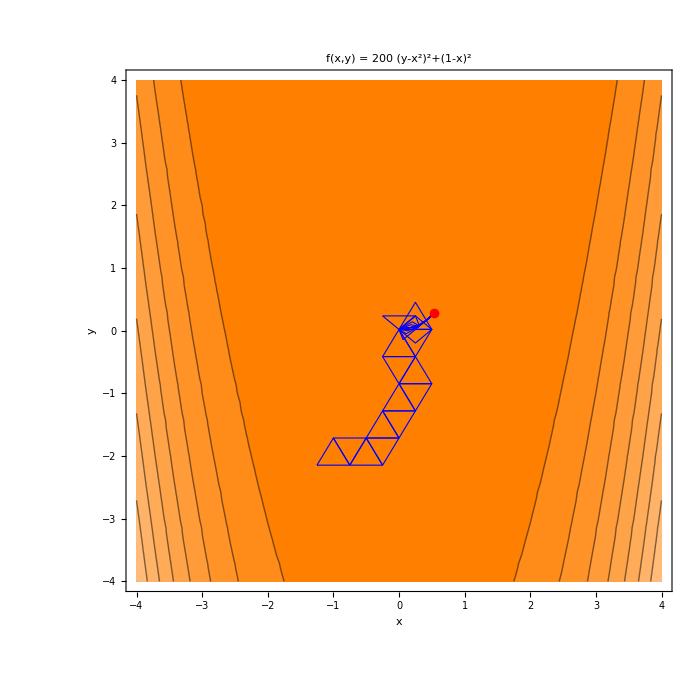

```mathematica
Show[ContourPlot[func[{x,y}],setX,setY,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5 #]],Lighter[Orange,0.5 #]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",func[{x,y}]}],Large](*,LabelStyle->Large*),FrameStyle->Thick,ImageSize->700],(*отрисовываем массив симплексов*)Table[Graphics[{FaceForm[],EdgeForm[Directive[Thick,Dashed,Blue]],Polygon[X[[i]]]}],{i,1,Length[X]}],Graphics[{Red,PointSize[0.01],Point[M[[1]]]}]]
```

```mathematica
iii[{x_,y_}]:=x;(*x≤0*)
point = {1,1};
```

```mathematica
g[point]+δ[iii,point,0.5]
```

127.166